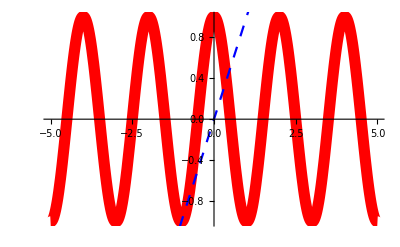

```mathematica
Clear[f,g,f1,g1]
f[x_]=Cos[π*x];
g[x_]=x;
f1=Plot[f[x],{x,-5,5},
PlotStyle->{RGBColor[1,0,0],
Thickness[0.02]},DisplayFunction->Identity];
g1=Plot[g[x],{x,-5,5},PlotStyle->{RGBColor[0,0,1],Dashing[{0.02}]},
DisplayFunction->Identity];
Show[f1,g1]
```